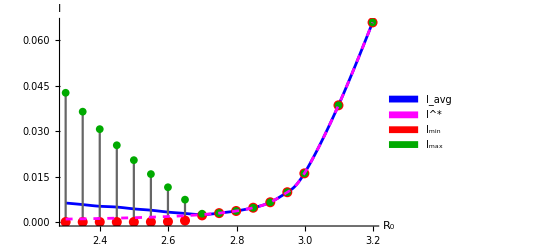

274.547

```mathematica
ClearAll["Global`*"]

(*Parameters that do not change across runs*)
Λ=0.0004;
μ=0.0004;
γ=1;

αI=0;
αR=0.0008;
ϵ=1;

tIn=0.;
tFin=1000.*52;
tStart=600.*52;

dt=0.2;                (*time step for sampling the numerical solution*)
lowFreqThreshold=0.1;  

betaList={2.3,2.35,2.4,2.45,2.5,2.55,2.6,2.65,2.7,2.75,2.8,2.85,2.9,2.95,3.,3.1,3.2};

(*------------------------------------------------------------*)
runForBeta[bet_?NumericQ]:=Module[{siirEquations,sol,timeSteps,Svals,Ivals,Rvals,fftData,n,freqs,validIdx,peakIdx,peakFreq,peakPeriod,iMin,iMax,tIMin,tIMax,plotSIR,plotFFT,halfIndex},siirEquations={S'[t]==Λ-bet*S[t]*I1[t]-μ*S[t],I1'[t]==bet*I1[t]*(S[t]+ϵ*R[t])-(γ+μ+αI)*I1[t],R'[t]==γ*I1[t]-ϵ*bet*R[t]*I1[t]-μ*R[t]-αR*R[t],S[0]==1-I1[0],I1[0]==10^-9,R[0]==0};
sol=Quiet@NDSolveValue[{siirEquations},{S,I1,R},{t,tIn,tFin},Method->{"BDF","MaxDifferenceOrder"->5},MaxSteps->Infinity,AccuracyGoal->12,PrecisionGoal->40];(*Sample solutions on a uniform grid in late time window*)
timeSteps=Range[tStart,tFin,dt];
Svals=sol[[1]]/@timeSteps;
Ivals=sol[[2]]/@timeSteps;
Rvals=sol[[3]]/@timeSteps;
fftData=Abs[Fourier[Svals]]^2;
n=Length[Svals];
freqs=Table[(k-1)/(n dt),{k,1,n}];
validIdx=Select[Range[2,n],freqs[[#]]<lowFreqThreshold&];
peakIdx=If[validIdx==={},Missing["NotAvailable"],validIdx[[First@Ordering[fftData[[validIdx]],-1]]]];
peakFreq=If[MissingQ[peakIdx],Missing["NotAvailable"],freqs[[peakIdx]]];
peakPeriod=Which[MissingQ[peakFreq],Missing["NoPeak"],peakFreq>0,1/peakFreq,True,Missing["NoPeak"]];
(*I(t) min/max with occurrence times*)
{iMin,iMax}={Min[Ivals],Max[Ivals]};
tIMin=timeSteps[[First@Ordering[Ivals,1]]];
tIMax=timeSteps[[First@Ordering[Ivals,-1]]];
(*Plots*)
plotSIR=Plot[Evaluate[{sol[[1]][t],sol[[2]][t],sol[[3]][t]}],{t,tIn,tFin},PlotRange->All,PlotStyle->{Blue,Red,Green},PlotLegends->{"S(t)","I(t)","R(t)"},AxesLabel->{"t","fraction of population"},PlotLabel->Row[{"Time Series (β = ",NumberForm[bet,{4,2}],")"}]];
halfIndex=Ceiling[n/2];(*show up to Nyquist*)plotFFT=ListPlot[Transpose[{freqs[[2;;halfIndex]],fftData[[2;;halfIndex]]}],Joined->True,PlotStyle->Red,AxesLabel->{"Frequency","Power"},PlotLabel->Row[{"FFT of S(t) — β = ",NumberForm[bet,{4,2}],If[NumericQ[peakPeriod],Row[{"  (Estimated period ≈ ",NumberForm[peakPeriod,{6,2}]," time units)"}],""]}],GridLines->Automatic];
<|"β"->bet,"Solution"->sol,"TimeSteps"->timeSteps,"Svals"->Svals,"Ivals"->Ivals,"Rvals"->Rvals,"PeakFrequency"->peakFreq,"PeakPeriod"->peakPeriod,"Imin"->iMin,"Imax"->iMax,"tImin"->tIMin,"tImax"->tIMax,"PlotSIR"->plotSIR,"PlotFFT"->plotFFT|>];

(*Run for all betas*)
results=runForBeta/@betaList;

(*------------------------------------------------------------*)
(*Display:1) plots for each β,2) a compact summary table*)
(*------------------------------------------------------------*)

(* Print["\n=== Time-Series & FFT Plots by β ===\n"];*)
Column[Table[Column[{results[[k,"PlotSIR"]],results[[k,"PlotFFT"]]},Spacings->1.25],{k,Length[results]}],Spacings->2];

(*Print["\n=== Summary (late-time, t ≥ ",tStart,") ===\n"];*)

summaryRows=Prepend[Table[With[{r=results[[k]]},{NumberForm[r["β"],{4,2}],If[NumericQ[r["PeakFrequency"]],NumberForm[r["PeakFrequency"],{8,6}],"—"],If[NumericQ[r["PeakPeriod"]],NumberForm[r["PeakPeriod"],{8,2}],"—"],NumberForm[r["Imin"],{8,6}],NumberForm[r["Imax"],{8,6}],NumberForm[r["tImin"],{8,1}],NumberForm[r["tImax"],{8,1}]}],{k,Length[results]}],{"β","Peak freq","Est. period","I min","I max","t at I min","t at I max"}];

Grid[summaryRows,Frame->All,Spacings->{2,1}];

(* ===Infection-only I(t) plots by β (late-time)===*)
(*Print["\n=== Infection-only I(t) (late-time) by β ===\n"];*)

infectionPlots=Table[Plot[results[[k,"Solution"]][[2]][t],{t,tStart,tFin},PlotRange->All,PlotStyle->Red,PlotLegends->{"I(t)"},AxesLabel->{"t","fract. of initial pop."},PlotLabel->Row[{"Infection I(t) — β = ",NumberForm[betaList[[k]],{4,2}]}]],{k,Length[results]}];

Column[infectionPlots,Spacings->1.25];

(* ===Average of I(t) over one estimated period (late time)===*)avgIOverLastPeriod[solution_,T_]:=Module[{t0},If[NumericQ[T]&&T>0,t0=tFin-T;
Quiet@Check[NIntegrate[solution[[2]][t],{t,t0,tFin},Method->{"LocalAdaptive"},MaxRecursion->10]/T,Missing["IntegrationFailed"]],Missing["NoPeriod"]]];

(*----Multi-β branch:uses `results` if it exists and is a nonempty list----*)
If[ValueQ[results]&&ListQ[results]&&results=!={},

avgITable=Prepend[Table[With[{r=results[[k]],T=results[[k,"PeakPeriod"]]},With[{avg=avgIOverLastPeriod[r["Solution"],T]},{NumberForm[r["β"],{4,2}],If[NumericQ[T],NumberForm[T,{6,2}],"—"],If[NumericQ[avg],NumberForm[avg,{8,6}],"—"]}]],{k,Length[results]}],{"β","Estimated period","Avg I over last period"}];
(*Print@Grid[avgITable,Frame->All,Spacings->{2,1}];*)
];

(*----Single-β fallback:uses `sol` and `peakPeriod` if present----*)
If[(!ValueQ[results]||results==={})&&ValueQ[sol]&&ValueQ[peakPeriod],Module[{avg=avgIOverLastPeriod[sol,peakPeriod]},Print["Avg I over last period: ",If[NumericQ[avg],NumberForm[avg,{8,6}],"—"],"  (T = ",If[NumericQ[peakPeriod],NumberForm[peakPeriod,{6,2}],"—"],")"];];];

Apar=γ+μ+αI;
r0Of[bet_?NumericQ]:=N[(bet*(Λ/μ))/Apar];

Table[{results[[k,"β"]],r0Of[results[[k,"β"]]]},{k,Length[results]}];

endemicIFromBetaViaR0[bet_?NumericQ]:=Module[{R0=r0Of[bet],a,b,c,disc,Ipos},a=ϵ bet^2 (μ+αI);
b=bet*(Apar (μ+αR)+ϵ μ (μ+αI)-ϵ R0 Apar μ);
c=(μ+αR) (Apar μ (1-R0));
disc=b^2-4 a c;
If[disc<=0,Return[Missing["NoEquilibrium"]]];
Ipos=(-b+Sqrt[disc])/(2 a);  (*positive branch*)
If[Ipos>0,Ipos,Missing["NoEquilibrium"]]
];


(*Avg I vs R0*)
avgPairsR0=Table[Module[{r=results[[k]],avg,R0},avg=avgIOverLastPeriod[r["Solution"],r["PeakPeriod"]];
R0=r0Of[r["β"]];
{R0,avg}],{k,Length[results]}];

dataAvgR0=SortBy[Select[avgPairsR0,NumericQ[#[[2]]]&],First];

avgCurveR0=ListLinePlot[dataAvgR0,InterpolationOrder->3,PlotRange->All,PlotStyle->Blue,AxesLabel->{Subscript[Style["R",FontFamily->"jsMath-cmsy10",FontSize->14],0],Style["I",Italic,FontFamily->"Times New Roman",FontSize->14]}];

(*I Min/Max vs R0*)
dataMinR0=Table[{r0Of[results[[k,"β"]]],results[[k,"Imin"]]},{k,Length[results]}];
dataMaxR0=Table[{r0Of[results[[k,"β"]]],results[[k,"Imax"]]},{k,Length[results]}];

vLinesR0=Table[With[{R0=r0Of[results[[k,"β"]]],ymin=results[[k,"Imin"]],ymax=results[[k,"Imax"]]},If[NumericQ[ymin]&&NumericQ[ymax],Line[{{R0,ymin},{R0,ymax}}],Sequence[]]],{k,Length[results]}];

overlayR0=Graphics[{GrayLevel[.4],Thickness[.004],vLinesR0,Red,PointSize[.018],Point[dataMinR0],Darker[Green],PointSize[.014],Point[dataMaxR0]}];

(*I^*vs R0*)
dataIstarR0=SortBy[Select[Table[{r0Of[results[[k,"β"]]],endemicIFromBetaViaR0[results[[k,"β"]]]},{k,Length[results]}],NumericQ[#[[2]]]&],First];

plotIstarR0=ListLinePlot[dataIstarR0,InterpolationOrder->3,PlotRange->All,PlotStyle->{Magenta,Dashed},AxesLabel->{"R0","I^*"},PlotLabel->"Endemic I* vs R0"];

legend=Placed[SwatchLegend[{Blue,Magenta,Red,Darker[Green]},{Style["I_avg",FontFamily->"Times New Roman"],Style["I^*",FontFamily->"Times New Roman"],Style["I_min",FontFamily->"Times New Roman"],Style["I_max",FontFamily->"Times New Roman"]},LegendFunction->(Framed[#,RoundingRadius->0,Background->White]&)],{{0.6, 0.7}, {0.5, 0.5}}];

plotAvgMinMaxLegend=Legended[Show[avgCurveR0,overlayR0,plotIstarR0],legend];
plotAvgMinMaxLegend

TimeUsed[]
```

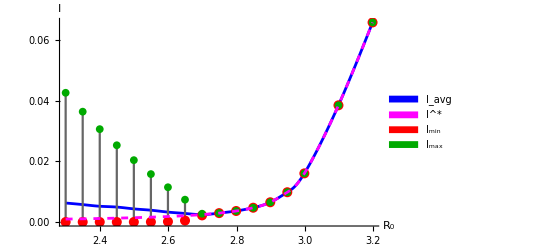

```mathematica
myPlotDupe=Out[79];

(*Edit the duplicate*)
customXTicks=Table[{x,Framed[NumberForm[x,{Infinity,1}],FrameStyle->None,FrameMargins->{{0,0},{0,4}}], {0, -0.015}},{x,2.4,3.2,0.2}];
customYTicks=Table[{y,Framed[NumberForm[y,{Infinity,2}],FrameStyle->None,FrameMargins->{{0,4},{0,0}}], {0, -0.015}},{y,0,0.07,0.01}];
Show[myPlotDupe,AxesOrigin->{2.26,-0.003}, GridLines->None, Ticks->{customXTicks, customYTicks}, AxesStyle->Thickness[0.003], TickDirection->"Outward"]
```

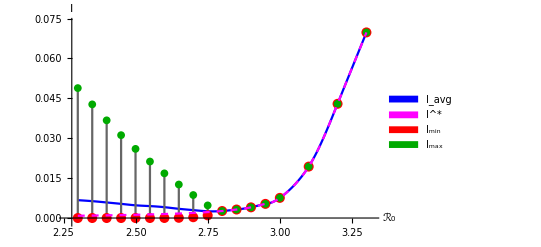

601.077